```mathematica
(*What we already knew*)
```

```mathematica
δa[r_]=(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3);α=1;
Vs1[r_]=- α/r Erf[r/(√2 a)]+c1 a^2 δa[r]
Vs2[r_]=- α/r Erf[r/(√2 a)]+c2 a^2 δa[r]+d1 a^4 Laplacian[δa[r],{r,θ,ϕ},"Spherical"]
```

(c1 ⅇ^(-r^2/(2 a^2)))/(2 √2 a π^(3/2))-Erf[r/(√2 a)]/r

(c2 ⅇ^(-r^2/(2 a^2)))/(2 √2 a π^(3/2))+a^4 d1 (-(3 ⅇ^(-r^2/(2 a^2)))/(2 √2 a^5 π^(3/2))+(ⅇ^(-r^2/(2 a^2)) r^2)/(2 √2 a^7 π^(3/2)))-Erf[r/(√2 a)]/r

```mathematica
a=1;
```

```mathematica
V[r_]=-(1/r)-(1.0415223038416566 E^(-0.9990999998788636 r))/r;
```

```mathematica
Module[{shift=10,d=2000,n=20,ev},{ev,ef}=NDEigensystem[{shift f[r]+V[r] f[r]-1/2 f''[r](*+NeumannValue[0,r==d]*),DirichletCondition[f[r]==0,True]},f[r],{r,0,d},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];
evShifted=ev-shift]
```

```mathematica
evShifted={-1.3373203533772653,-0.18643394310640815,-0.07105746371822974,-0.037407168791812495,-0.023050971814825516,-0.01561839001324472,-0.01127779477469204,-0.008524333162924336,-0.006668809821686494,-0.005359292793286841,-0.004400800990534748,-0.003678219961269491,-0.0031200305705318954,-0.0026798978946942498,-0.0023267324917313204,-0.0020390441242952306,-0.0018015927858030523,-0.001603327672349053,-0.0014360776077175785,-0.0012936953465683132}
```

{-1.33732,-0.186434,-0.0710575,-0.0374072,-0.023051,-0.0156184,-0.0112778,-0.00852433,-0.00666881,-0.00535929,-0.0044008,-0.00367822,-0.00312003,-0.0026799,-0.00232673,-0.00203904,-0.00180159,-0.00160333,-0.00143608,-0.0012937}

```mathematica
LδE={{1.3373202085701266,0.33732020857012657},{0.18643393369537004,0.25426426521851986},{0.07105746158595466,0.360482845726408},{0.037407167983470095,0.4014853122644785},{0.023050971424107496,0.42372571439731266},{0.015618389794715332,0.437737967390248},{0.005359292748188737,0.7373946553387517},{0.001293695341342178,0.9172034981541006}};
Lδϵ={{1.3373202085701266,0.5741276779047597},{0.18643393369537004,0.1051516432644786},{0.07105746158595466,0.037300022830719023},{0.037407167983470095,0.0189380005149714},{0.023050971424107496,0.011162659074988026},{0.015618389794715332,0.007167940071927817},{0.005359292748188737,0.0018188435094718296},{0.001293695341342178,0.}};
```

```mathematica
(*Fit of c1*)
```

```mathematica
c1d0=FindRoot[f[evShifted[[20]],c1][1.*10^-9]==0/.With[{r1=10^-10,r2=2000},ParametricNDSolve[{(Vs1[r]) f[r]-1/2 f''[r]==e f[r],f[r2]==0,f'[r2]==-r1},f,{r,r2,r1},{e,c1}]],{c1,-10,-50},MaxIterations->1000]
```

FindRoot::cvmit: 无法在 1000 次迭代中收敛到要求的准确度或者精度.

{c1→-44.2918}

```mathematica
c1d0={c1->-44.291};
sol=With[{r1=10^-10,r2=2000},ParametricNDSolve[{(Vs1[r]/.c1d0) f[r]-1/2 f''[r]==e f[r],f[r2]==0,f'[r2]==-r1},f,{r,r2,r1},e]];
FindRoot[f[e][10^-10]==0/.sol,{e,-0.0012,-0.0013}]
((e/.%)-evShifted[[20]])/evShifted[[20]]
```

{e→-0.00129369}

-1.09589×10^-6

```mathematica
Module[{shift=10,d=2000,n=20,evc1},{evc1,efc1}=NDEigensystem[{shift f[r]+(Vs1[r]/.c1d0) f[r]-1/2 f''[r](*+NeumannValue[0,r==d]*),DirichletCondition[f[r]==0,True]},f[r],{r,0,d},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.01}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];
evShiftedc1=evc1-shift]
```

```mathematica
{-1.457065698258475,-0.18646012436361303,-0.07113316468056041,-0.037424340905353404,-0.023056199202599714,-0.015620344301947142,-0.0112786365817783,-0.008524734271198042,-0.006669015539223722,-0.005359404157463388,-0.0044008636700496595,-0.0036782561750179354,-0.003120051789153422,-0.002679910334524749,-0.002326739659444854,-0.0020390480665959387,-0.001801594729542444,-0.0016033283705461088,-0.001436077531177915,-0.0012936947941923904}
```

{-1.45707,-0.18646,-0.0711332,-0.0374243,-0.0230562,-0.0156203,-0.0112786,-0.00852473,-0.00666902,-0.0053594,-0.00440086,-0.00367826,-0.00312005,-0.00267991,-0.00232674,-0.00203905,-0.00180159,-0.00160333,-0.00143608,-0.00129369}

```mathematica
(*Fit of c2 and d1*)
```

```mathematica
c2d1={c2->-53.15,d1->-6.015};
sol=With[{r1=10^-10,r2=2000},ParametricNDSolve[{(Vs2[r]/.c2d1) f[r]-1/2 f''[r]==e f[r],f[r2]==0,f'[r2]==-r1},f,{r,r2,r1},e]];
FindRoot[f[e][10^-10]==0/.sol,{e,-0.0012,-0.0013}];
((e/.%)-evShifted[[20]])/evShifted[[20]]
FindRoot[f[e][10^-9]==0/.sol,{e,-0.0053,-0.0054}];
((e/.%)-evShifted[[10]])/evShifted[[10]]
```

4.91217×10^-6

0.0000681183

```mathematica
FindRoot[{f[evShifted[[10]],c2,d1][10^-10]==0(*,f[evShifted[[15]],c2,d1][10^-10]==0*),f[evShifted[[20]],c2,d1][10^-10]==0}/.With[{r1=10^-10,r2=2000},ParametricNDSolve[{(Vs2[r]) f[r]-1/2 f''[r]==e f[r],f[r2]==0,f'[r2]==-r1},f,{r,r2,r1},{e,c2,d1}]],{{d1,-6.},{c2,-53}},WorkingPrecision->20,AccuracyGoal->6,PrecisionGoal->6]
sol=With[{r1=10^-10,r2=2000},ParametricNDSolve[{(Vs2[r]/.%) f[r]-1/2 f''[r]==e f[r],f[r2]==0,f'[r2]==-r1},f,{r,r2,r1},e]];
FindRoot[f[e][10^-9]==0/.sol,{e,-0.0053,-0.0054}];
((e/.%)-evShifted[[10]])/evShifted[[10]]
FindRoot[f[e][10^-10]==0/.sol,{e,-0.0012,-0.0013}];
((e/.%)-evShifted[[20]])/evShifted[[20]]
```

{d1→-6.,c2→-53.}

-0.000295211

-0.000173022

```mathematica
{c2->-53.118003972444555,d1->-6.}
```

```mathematica
(*An alternative option with accuracy of 10^-8 in 15S but quickly increase to 10^-6 from 16S to 20S*)
{d1->-6.20693679739979323404740856597133865245`20.,c2->-53.4399999999999977262632455676794052124`20.}
```

```mathematica
Module[{shift=10,d=2000,n=20,evc2},{evc2,efc2}=NDEigensystem[{shift f[r]+(Vs2[r]/.{c2->-40.68550396037793271110464724852347263141`20.,d1->2.692471822821146711574860760345708796726126546337616101571`20.}(*{c2->-46.33062759418801083400760936759136764569`20.,d1->-1.4507240422854862740772183829308862534640647271750179582521`20.}*)(*{c2->-40.67794727611782987995687250097809106016`20.,d1->2.6983043145447927002450034379127825343275667350359851097712`20.}*)) f[r]-1/2 f''[r](*+NeumannValue[0,r==d]*),DirichletCondition[f[r]==0,True]},f[r],{r,0,d},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.01}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];
evShiftedc2=evc2-shift]
```

```mathematica
{-1.536729911101066,-0.18512561846669584,-0.07102901325784572,-0.0374045610520497,-0.02305054264886408,-0.015618292014920598,-0.011277767326479449,-0.0085243243899491,-0.006668806777785363,-0.005359291693650903,-0.004400800595309562,-0.0036782198297622415,-0.003120030538262597,-0.002679897896538108,-0.0023267325023503815,-0.002039044135148771,-0.0018015927934449394,-0.00160332767624638,-0.0014360776086768112,-0.0012936953455060518}
```

{-1.53673,-0.185126,-0.071029,-0.0374046,-0.0230505,-0.0156183,-0.0112778,-0.00852432,-0.00666881,-0.00535929,-0.0044008,-0.00367822,-0.00312003,-0.0026799,-0.00232673,-0.00203904,-0.00180159,-0.00160333,-0.00143608,-0.0012937}

```mathematica
δEVs1=Abs[(evShiftedc1-evShifted)/evShifted]
δEVs2=Abs[(evShiftedc2-evShifted)/evShifted]
```

{0.0895413,0.000140432,0.00106535,0.000459059,0.000226775,0.000125127,0.0000746429,0.0000470545,0.0000308477,0.0000207796,0.0000142428,9.84545×10^-6,6.80077×10^-6,4.6419×10^-6,3.08059×10^-6,1.93341×10^-6,1.0789×10^-6,4.35467×10^-7,5.32977×10^-8,4.26975×10^-7}

{0.149111,0.00701763,0.000400387,0.0000697123,0.0000186181,6.27455×10^-6,2.43383×10^-6,1.02917×10^-6,4.56438×10^-7,2.05183×10^-7,8.98076×10^-8,3.5753×10^-8,1.03426×10^-8,6.88033×10^-10,4.56394×10^-9,5.32286×10^-9,4.24174×10^-9,2.43077×10^-9,6.67953×10^-10,8.21106×10^-10}

```mathematica
δEVs1=Abs[(%42-evShifted)/evShifted]
δEVs2=Abs[(%43-evShifted)/evShifted]
```

{0.0895413,0.000140432,0.00106535,0.000459059,0.000226775,0.000125127,0.0000746429,0.0000470545,0.0000308477,0.0000207796,0.0000142428,9.84545×10^-6,6.80077×10^-6,4.6419×10^-6,3.08059×10^-6,1.93341×10^-6,1.0789×10^-6,4.35467×10^-7,5.32977×10^-8,4.26975×10^-7}

{0.149111,0.00701763,0.000400387,0.0000697123,0.0000186181,6.27455×10^-6,2.43383×10^-6,1.02917×10^-6,4.56438×10^-7,2.05183×10^-7,8.98076×10^-8,3.5753×10^-8,1.03426×10^-8,6.88033×10^-10,4.56394×10^-9,5.32286×10^-9,4.24174×10^-9,2.43077×10^-9,6.67953×10^-10,8.21106×10^-10}

```mathematica
LδEVs1=Transpose@({-evShifted}~Join~{δEVs1});
LδEVs2=Transpose@({-evShifted}~Join~{δEVs2});
```

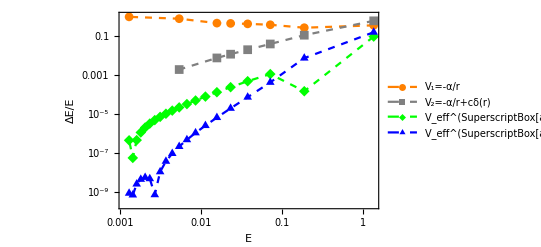

```mathematica
ListLogLogPlot[{LδE,Lδϵ,LδEVs1,LδEVs2},Frame->True,Joined->True,PlotMarkers->Automatic,ImageSize->Full,FrameLabel->{"E","ΔE/E"},RotateLabel->False,PlotStyle->{{Dashed,Orange},{Dashed,Gray},{Dashed,Green},{Dashed,Blue}},PlotLegends->{"V_1=-α/r","V_2=-α/r+cδ(r)","V_eff^(SuperscriptBox[a, 2])","V_eff^(SuperscriptBox[a, 4])"}]
Export["C:\\Users\\ASUS\\OneDrive\\文档\\Test_6\\Test_CurveFitting1_Figure2.eps",%];
```

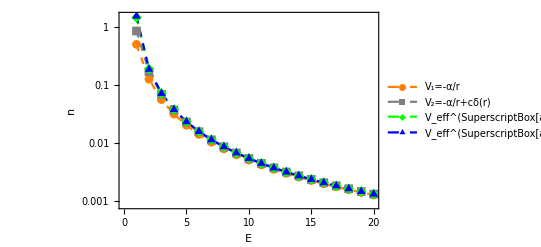

```mathematica
ListLogPlot[{Table[1/(2 n^2),{n,20}],-Table[-1/(2 n^2)+-0.6195838082285936/(√π n^3),{n,20}],-%42,-%43},Frame->True,Joined->True,PlotMarkers->Automatic,FrameLabel->{"E","n"},RotateLabel->False,PlotStyle->{{Dashed,Orange},{Dashed,Gray},{Dashed,Green},{Dashed,Blue}},PlotLegends->{"V_1=-α/r","V_2=-α/r+cδ(r)","V_eff^(SuperscriptBox[a, 2])","V_eff^(SuperscriptBox[a, 4])"},ImageSize->Full]
Export["C:\\Users\\ASUS\\OneDrive\\文档\\Test_6\\Test_CurveFitting1_Figure2_1.eps",%];
```

```mathematica
(*Export with only 0.01 grid*)
```

```mathematica
Export["C:\\Users\\ASUS\\Documents\\TestDATA_evShiftedVs2.dat",evShiftedc2,"Table"];
```

```mathematica
Export["C:\\Users\\ASUS\\Documents\\TestDATA_efVs2.dat",efc2,"Table"];
```

```mathematica
Export["C:\\Users\\ASUS\\Documents\\TestDATA_evShiftedVs1.dat",evShiftedc1,"Table"];
```

```mathematica
Export["C:\\Users\\ASUS\\Documents\\TestDATA_efVs1.dat",efc1,"Table"];
```